# 连续线绘图

用连续线绘图表示列奥纳多·达·芬奇的蒙娜·丽莎 .

```mathematica
monalisa=Entity["Artwork","MonaLisa::LeonardoDaVinci"][EntityProperty["Artwork","Image"]]
```

-Graphics-

```mathematica
monalisa = -Graphics-;
```

将图像转换成点 .

```mathematica
monalisa=ColorQuantize[ColorConvert[monalisa,"Grayscale"],2];
```

```mathematica
pos=PixelValuePositions[ImageAdjust[monalisa],0];
```

绘制蒙娜·丽莎 .

```mathematica
res=FindShortestTour[pos];
```

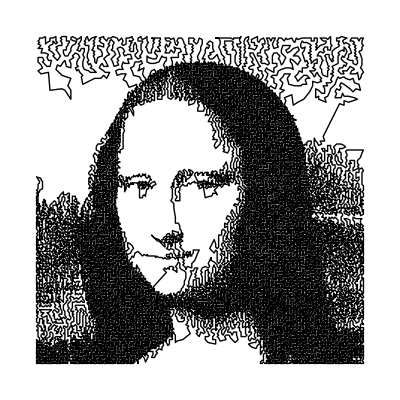

```mathematica
Graphics[Line[pos[[res[[2]]]]]]
```